# 🎱 Quantum Walks in Billiards: A Beginner’s Guide

Welcome! In this notebook, we will simulate a Discrete-Time Quantum Walk (DTQW) inside a 2D billiard geometry. If you are familiar with a particle in a box from quantum mechanics, imagine that particle moving on a discrete grid, carrying an internal “coin” (spin) that tells it which way to turn.

We will use the QuantumWalks library to handle the complex linear algebra efficiently.

## 1. Setup and Initialization

First, we need to load our library. > Note: Make sure the QuantumWalks folder is in a location Mathematica can see (like FileNameJoin[{$UserBaseDirectory, “Applications”}]) or allows the kernel to find it.

```mathematica
(*Load the QutumWalks package*)
<<QuantumWalks`
<<QMB`
```

## 2. Defining the Geometry

First you must decide one of these geometries:

Rectangle (integrable)

Ellipse (integrable)

Bunimovich (chaotic), you may choose to work in the dessymetrized or full stadium

Sinai (chaotic), you may choose to work in the dessymetrized or full billiard

Cardiod (chaotic), only full billiard available for now

Let us choose the Bunimovich dessymetrized billiard. First we must generate the basis for the position grid space:

```mathematica
?GenerateFullStadiumBasis
```

Total number of grid points (N): 2711

Total Hilbert Space Dimension (2N): 5422

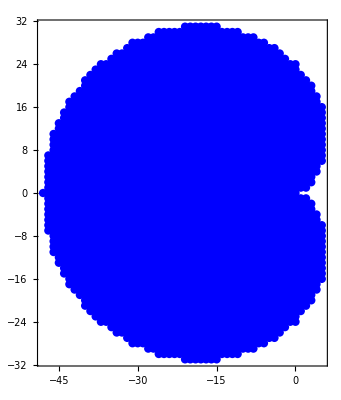

```mathematica
(*Define geometry parameters*)
xc=38; (*Length of the straight part*)
nu=xc;  (*Radius (width)*)

(*Generate the grid data*)
(*billiardData=GenerateStadiumBasis[xc,nu];*)
(*billiardData=GenerateFullStadiumBasis[xc,nu];*)
billiardData=GenerateCardioidBasis[12];
(*billiardData=GenerateSinaiBasis[120,75];
billiardData=GenerateRectangleBasis[60,40];*)

(*Let's see what we built*)
Print["Total number of grid points (N): ",billiardData["Dimension"]];
Print["Total Hilbert Space Dimension (2N): ",2*billiardData["Dimension"]];

(*Visualize the grid*)
ListPlot[billiardData["Coords"],PlotStyle->{PointSize[0.015],Blue},AspectRatio->Automatic,Frame->True]
```

## 3. Building the Operators

For a 2D walk, we need:

The Coin (C): Rotates the internal spin state.

The Shift operators (S_x, S_y): Move the particle Left/Right and Up/Down based on its spin.

The library function BuildShiftOperators does the heavy lifting of handling boundary conditions (bouncing off walls) using Sparse Arrays to save memory.

```mathematica
(*1. Construct Shift Operators*)
(*Returns a list {Wm,Wn}*)
{Sx,Sy}=BuildShiftOperators[billiardData];

(*2. Construct the Coin Operator*)
(*We use a standard Hadamard-like coin with angle Pi/4*)
dim=billiardData["Dimension"];
Coin1=Coin[Pi/4.,dim];
Coin2=Coin[Pi+0.1,dim];

(*{θ1,θ2}=RandomReal[{0,2Pi},2];
Coin1=Coin[θ1,dim];
Coin2=Coin[θ2,dim];*)

(*Check if the operators are Unitary (Preserve probability)*)
(*This is a good physics check!*)
unitaryCheck=UnitaryMatrixQ[Sy]&&UnitaryMatrixQ[Sx]&&UnitaryMatrixQ[Coin1]&&UnitaryMatrixQ[Coin2];
Print["Are our operators valid unitary matrices? ",unitaryCheck];
```

Are our operators valid unitary matrices? True

```mathematica
Differences[Mod[Coin[Pi+0.1,1]//Eigenvalues//Arg,2Pi]]
```

{0.809179}

```mathematica
Subdivide[0,2Pi,8]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

## 4. The Evolution Operator

A single time step (U) in a 2D Split-Step Quantum Walk is often defined as: ψ_(t+1)=S_x C_2 S_y C_1

This means: Flip the coin, then Move vertrically, flip once again the coin, then Move Vertically.

```mathematica
(*Define the single step evolution operator*)
U=Sx.Coin2.Sy.Coin1
```

SparseArray[…]

```mathematica
U=Sy.Coin2.Sx.Coin1
```

SparseArray[…]

### 4.1 Level statistics

#### θ_1=θ_2=π/4

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

```mathematica
{evals,evecs}=Transpose[SortBy[Transpose[Eigensystem[Normal[U]]],First]];
eigenphases=Sort@Mod[Arg[evals],2Pi];
```

```mathematica
Chop[evecs[[1]]]
Reverse[KroneckerProduct[IdentityMatrix[11],Pauli[1]].Chop[evecs[[1]]]]
```

{-0.0844425,0.216183+0.248079 ⅈ,0.383438,0.0963434-0.236913 ⅈ,-0.0225535-0.328283 ⅈ,-0.164102+0.187742 ⅈ,0.0319103-0.0319103 ⅈ,-0.201436-0.0200152 ⅈ,0.235648+0.0993976 ⅈ,-0.144881-0.0171574 ⅈ,-0.187742+0.164102 ⅈ,-0.0664867+0.146804 ⅈ,0.15659+0.128284 ⅈ,-0.152025-0.128721 ⅈ,0.0171574+0.144881 ⅈ,-0.0631991+0.152576 ⅈ,-0.056793+0.150819 ⅈ,-0.158452-0.132493 ⅈ,0.152025-0.128721 ⅈ,0.0162937+0.0393364 ⅈ,0.158452-0.132493 ⅈ,0.0164153+0.0396301 ⅈ}

{0.158452-0.132493 ⅈ,0.0164153+0.0396301 ⅈ,0.152025-0.128721 ⅈ,0.0162937+0.0393364 ⅈ,-0.056793+0.150819 ⅈ,-0.158452-0.132493 ⅈ,0.0171574+0.144881 ⅈ,-0.0631991+0.152576 ⅈ,0.15659+0.128284 ⅈ,-0.152025-0.128721 ⅈ,-0.187742+0.164102 ⅈ,-0.0664867+0.146804 ⅈ,0.235648+0.0993976 ⅈ,-0.144881-0.0171574 ⅈ,0.0319103-0.0319103 ⅈ,-0.201436-0.0200152 ⅈ,-0.0225535-0.328283 ⅈ,-0.164102+0.187742 ⅈ,0.383438+0. ⅈ,0.0963434-0.236913 ⅈ,-0.0844425+0. ⅈ,0.216183+0.248079 ⅈ}

```mathematica
billiardData["Mapping"][{-1,-1}*#]&/@billiardData["Coords"]
```

{11,10,9,8,7,6,5,4,3,2,1}

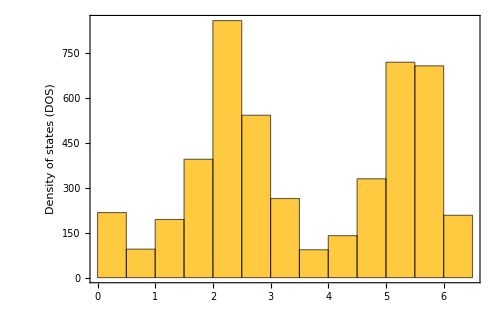

```mathematica
Histogram[eigenphases,Automatic,"Count",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

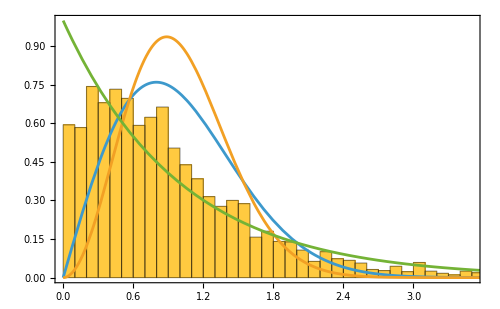

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

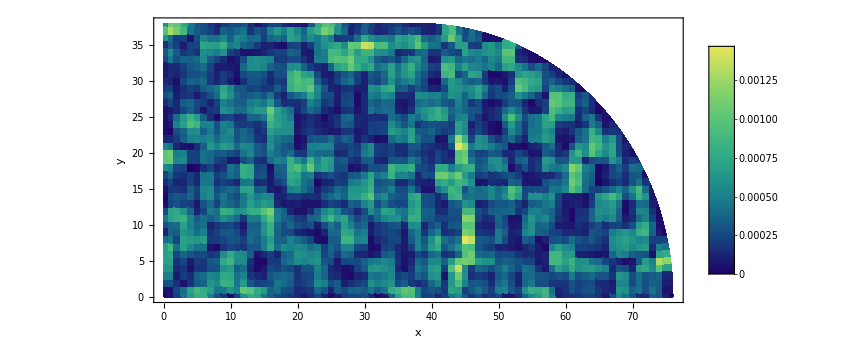

```mathematica
(*1. Extraemos parÃ¡metros.En Bunimovich.wl,"Params" es la lista {xc,nu}*){xcParameter,nuParameter}=billiardData["Params"];

(*2. Definimos la funciÃ.b3n lÃ.b3gica del Estadio (1/4 Desimetrizado)*)
StadiumRegionQ=Function[{x,y},Module[{inRectangle,inCircle},(*CondiciÃ.b3n 1:Parte rectangular (0<=x<=xc)*)inRectangle=(x<=xcParameter&&y<=nuParameter);
(*CondiciÃ.b3n 2:Parte circular (x>xc)*)(*Centrada en (xc,0) con radio nu*)inCircle=(x>xcParameter&&(x-xcParameter)^2+y^2<=nuParameter^2);
(*La regiÃ.b3n vÃ¡lida es la uniÃ.b3n de ambas,restringida al primer cuadrante*)(inRectangle||inCircle)&&(x>=0)&&(y>=0)]];

(*3. Generamos el Plot*)
ListDensityPlot[StateToPlotData[evecs[[4201]],billiardData["Coords"]],ColorFunction->"BlueGreenYellow",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,(*Recorte exacto usando la geometrÃa del estadio*)RegionFunction->Function[{x,y,z},StadiumRegionQ[x,y]],Background->None,FrameLabel->{"x","y"}]
```

```mathematica
Manipulate[
ListDensityPlot[StateToPlotData[evecs[[i]],billiardData["Coords"]],ColorFunction->"SunsetColors",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,(*Recorte exacto usando la geometrÃa del estadio*)RegionFunction->Function[{x,y,z},StadiumRegionQ[x,y]],Background->None,FrameLabel->{"x","y"}]
,{i,1600,1700}]
```

```mathematica
ipr=Table[Total[Total[Abs[evecs[[i,#;;#+1]]]^4]&/@Range[1,2*dim,2]],{i,2*dim}];
```

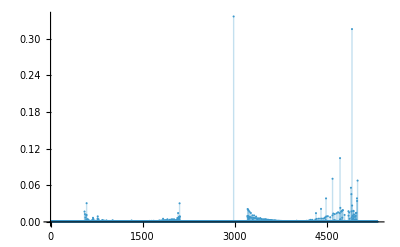

```mathematica
ListPlot[ipr,Filling->Axis,PlotRange->All]
```

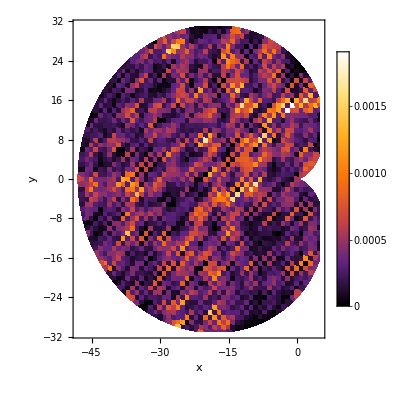

```mathematica
(*1. Extraemos el radio R de la metadata del billar*)
RParameter=billiardData["Params","R"];

(*2. Definimos la funciÃ.b3n lÃ.b3gica del Cardioide (Coordenadas Cartesianas)*)
(*r^2=x^2+y^2*)
CardioidRegionQ=Function[{x,y},Module[{r2=x^2+y^2},(r2+2*RParameter*x)^2<=4*RParameter^2*r2]];

(*3. Generamos el Plot con RegionFunction*)
ListDensityPlot[StateToPlotData[evecs[[148]],billiardData["Coords"]],ColorFunction->"SunsetColors",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0,(*Mantiene el aspecto de celdas/voronoi*)(*ESTA ES LA CLAVE:Recorta todo lo que no cumpla la ecuaciÃ.b3n*)RegionFunction->Function[{x,y,z},CardioidRegionQ[x,y]],(*Opcional:Asegura que el fondo del canvas sea transparente*)Background->None,FrameLabel->{"x","y"}]
```

Hay que filtrar los datos:

```mathematica
filteredEigenphases=Select[eigenphases,Round[1.7]<Round[#,10.^-9]<Round[2.7,10.^-9]&];
```

```mathematica
filteredEigenphases=Select[eigenphases,Round[Pi/4.,10.^-9]<Round[#,10.^-9]<Round[Pi+Pi/4.,10.^-9]&&Round[#,10.^-9]!=Round[Pi/4.+Pi/2.,10.^-9]&];
```

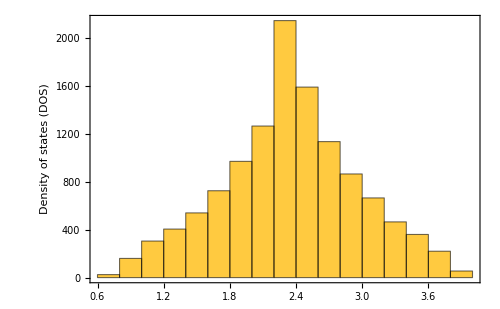

```mathematica
Histogram[filteredEigenphases,Automatic,"Intensity",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases];
```

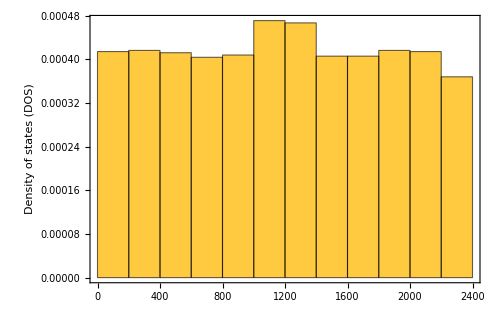

```mathematica
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

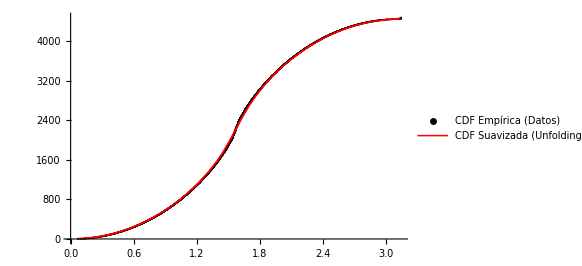

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
evals=unfoldedEigenphases["OriginalLevels"];
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[unfoldedEigenphases["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

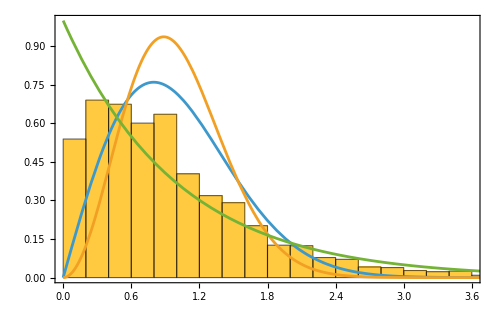

```mathematica
Show[
Histogram[Differences[unfoldedEigenphases["UnfoldedLevels"][[;;-200]]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

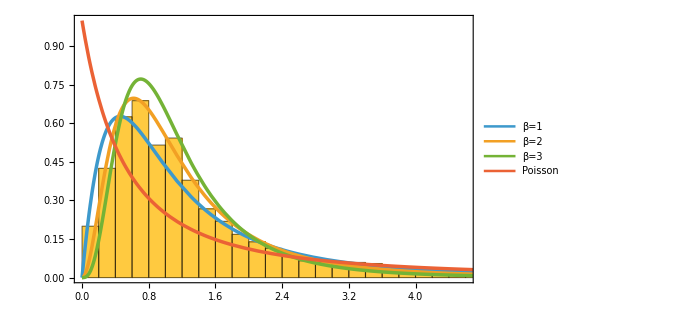

```mathematica
Show[
Histogram[SpacingRatios[filteredEigenphases,2],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[Append[RatiosDistribution[r,#]&/@Range[3],RatiosDistributionPoisson[r,1]]//Evaluate,{r,0,8.},PlotLegends->Placed[Append["β="<>ToString[#]&/@Range[3],"Poisson"],{Right,Top}],PlotStyle->Directive[Thickness[0.005],Opacity[1.]],LabelStyle->Directive[20],PlotRange->All]
]
```

```mathematica
Table[EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,1.],RatiosDistribution[#,β]&],{β,3}]
```

{0.0361626,0.0639077,0.173755}

```mathematica
Table[EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,2.],RatiosDistribution[#,β]&],{β,3}]
```

{0.226943,0.0932235,0.0370469}

#### θ_1=θ_2=π/4

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

```mathematica
Export["/home/jadeleon/Documents/libs/QuantumWalks/UsageExamples/data.wdx",evals]
```

/home/jadeleon/Documents/libs/QuantumWalks/UsageExamples/data.wdx

```mathematica
eigenphases=Import["/home/jadeleon/Documents/libs/QuantumWalks/UsageExamples/data.wdx"];
```

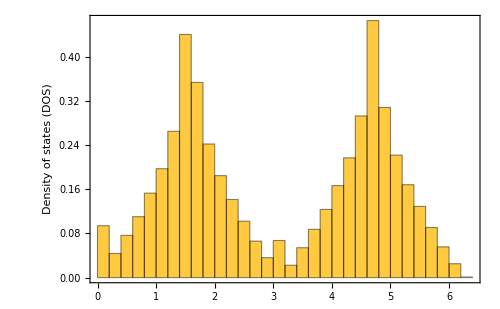

```mathematica
Histogram[eigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

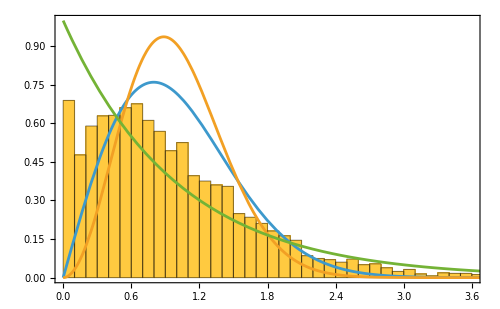

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

Hay que filtrar los datos:

```mathematica
filteredEigenphases=Select[evals,0.<Round[#,10.^-9]<Round[Pi,10.^-9]&];
```

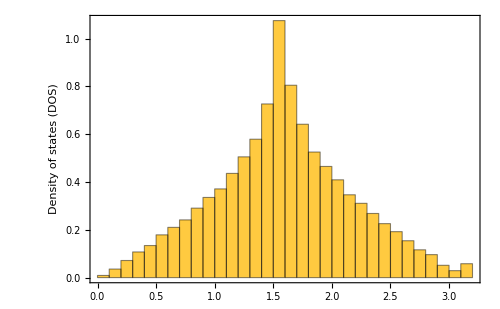

```mathematica
Histogram[filteredEigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases];
```

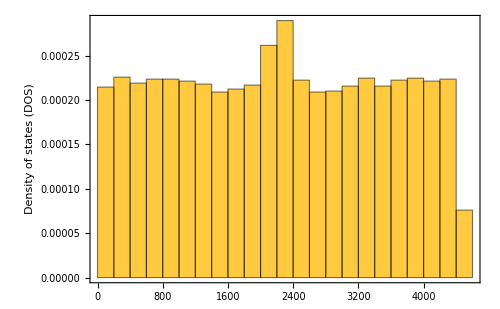

```mathematica
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

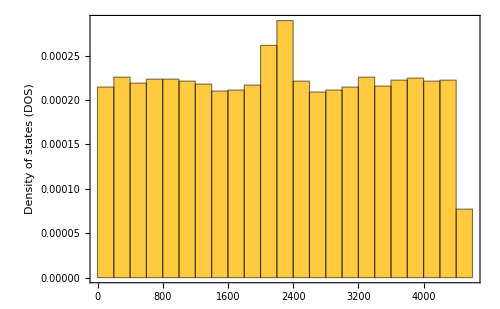

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases,"Bandwidth"->0.09];
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
evals=unfoldedEigenphases["OriginalLevels"];
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[unfoldedEigenphases["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

-Graphics-

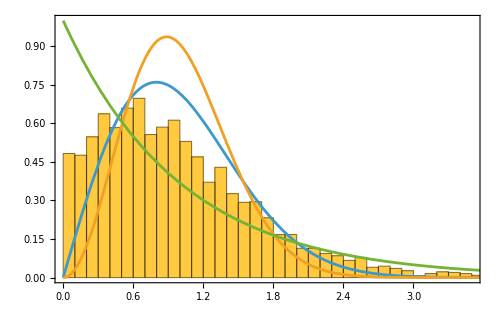

```mathematica
Show[
Histogram[Differences[unfoldedEigenphases["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

#### θ_1=π/4, θ_2=π/6

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

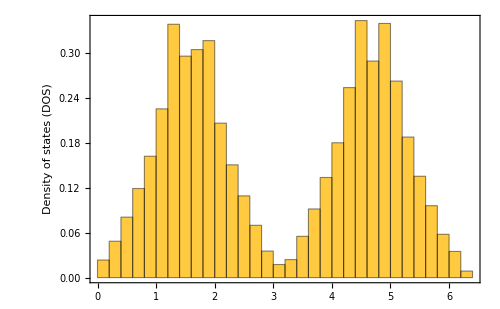

```mathematica
Histogram[eigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

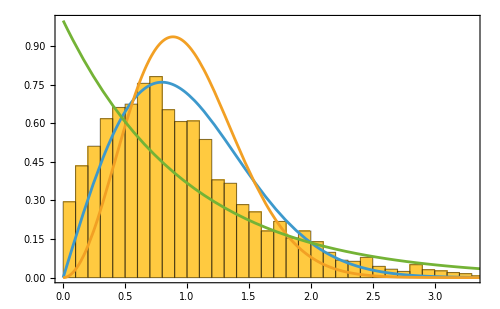

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

Filtrando las eigenfases:

```mathematica
filteredEigenphases=Select[eigenphases,0.<Round[#,10.^-9]<Round[Pi,10.^-9]&&Round[#,10.^-9]!=Round[Pi/2.,10.^-9]&];
```

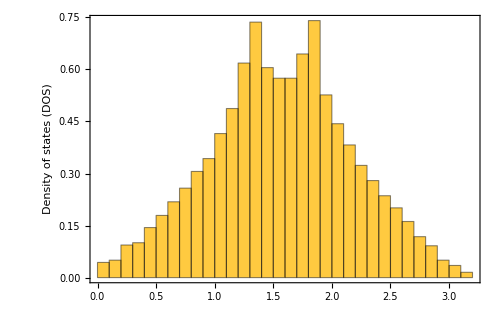

```mathematica
Histogram[filteredEigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases,"Bandwidth"->0.03];
```

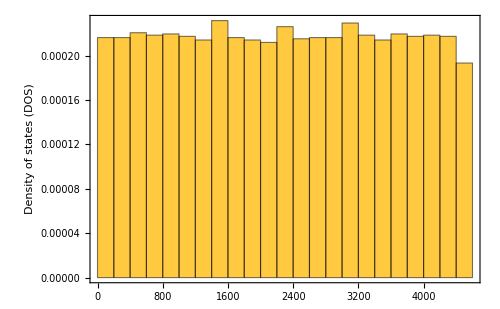

```mathematica
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
Table[
phasesTmp=Unfold[filteredEigenphases,"Bandwidth"->x];
{x,EmpiricalKLDivergence[phasesTmp["OriginalLevels"],phasesTmp["SmoothPDF"][#]&]}
,{x,0.01,0.1,0.01}]
```

{{0.01,0.00210147},{0.02,0.000394697},{0.03,0.000143662},{0.04,0.000213532},{0.05,0.000418566},{0.06,0.000688234},{0.07,0.000985788},{0.08,0.00129821},{0.09,0.00162189},{0.1,0.00195686}}

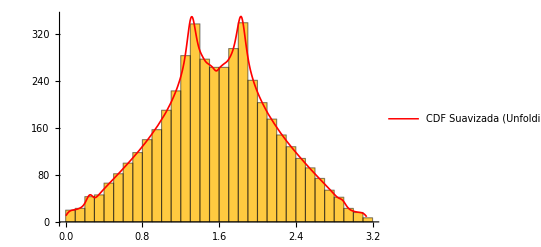

```mathematica
Show[
Histogram[filteredEigenphases,Automatic,"Count"],
Plot[unfoldedEigenphases["SmoothPDF"][e]/10,{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

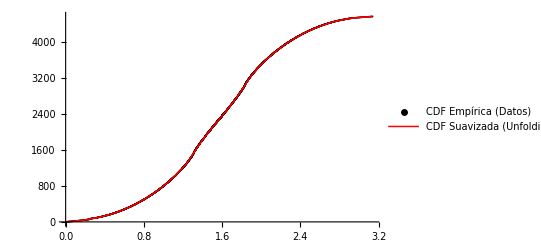

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
evals=unfoldedEigenphases["OriginalLevels"];
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[unfoldedEigenphases["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

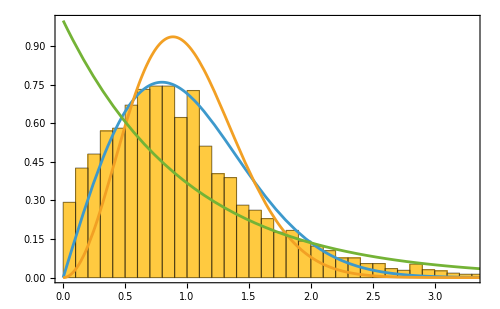

```mathematica
Show[
Histogram[Differences[unfoldedEigenphases["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

```mathematica
Table[EmpiricalKLDivergence[NormalizedSpacingRatios[filteredEigenphases,2],2*RatiosDistribution[#,N@β]&],{β,5}]
```

{0.107854,0.0235236,0.0175482,0.0516977,0.110262}

#### θ_1=θ_2=π/4 (rectángulo)

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

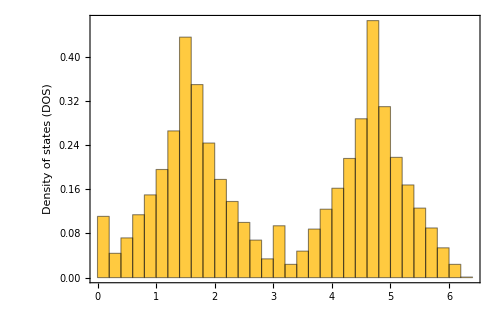

```mathematica
Histogram[eigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
Select[Tally[Chop@Sort[eigenphases]],#[[2]]>2&]
```

{{0,101},{3.14159,20}}

```mathematica
Pi/2.
```

1.5708

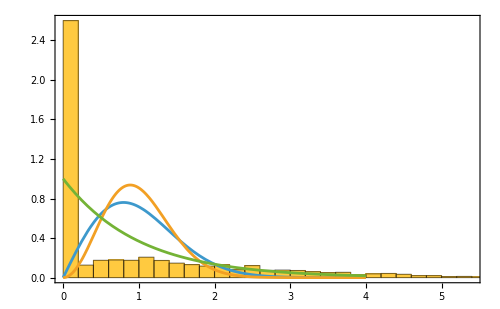

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"][[1000;;-1000]]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

Hay que filtrar los datos:

```mathematica
filteredEigenphases=Select[eigenphases,0.<Round[#,10.^-9]<Round[Pi,10.^-9]&&Round[#,10.^-9]!=Round[Pi/2.,10.^-9]&];
```

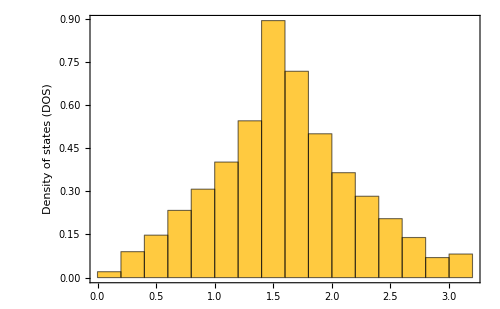

```mathematica
Histogram[filteredEigenphases,Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases];
```

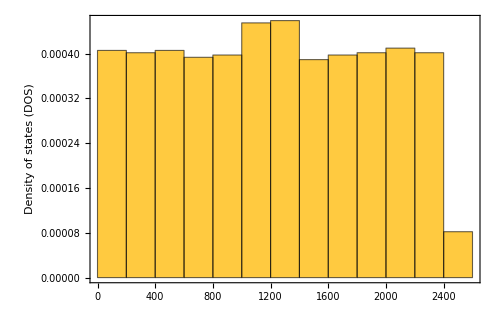

```mathematica
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

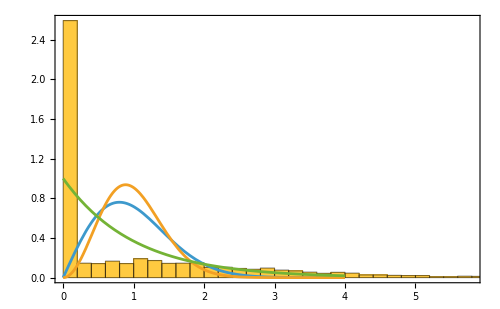

```mathematica
Show[
Histogram[Differences[unfoldedEigenphases["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

#### Random θ_1 and θ_2

```mathematica
(*Exact diagonalization to obtain eigenvalues*)
eigenphases=Mod[Arg[Eigenvalues[Normal[U]]],2Pi];
```

```mathematica
{evals,evecs}=Transpose[SortBy[Transpose[Eigensystem[Normal[U]]],First]];
eigenphases=Sort@Mod[Arg[evals],2Pi];
```

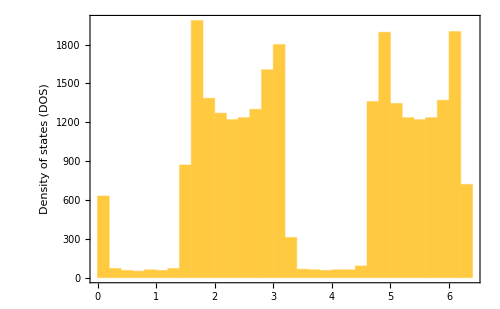

```mathematica
Histogram[eigenphases,Automatic,"Intensity",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

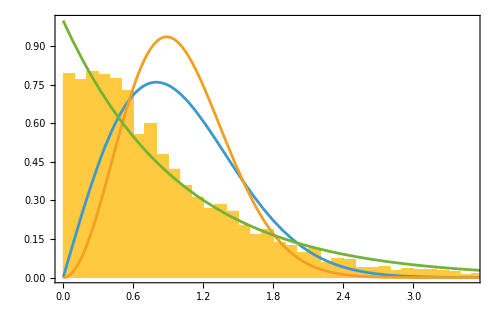

```mathematica
Show[
Histogram[Differences[Unfold[eigenphases]["UnfoldedLevels"]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

Hay que filtrar los datos:

```mathematica
filteredEigenphases=Select[eigenphases,Round[Pi/4.,10.^-9]<Round[#,10.^-9]<Round[Pi+Pi/4.,10.^-9]&&Round[#,10.^-9]!=Round[Pi/4.+Pi/2.,10.^-9]&];
```

```mathematica
filteredEigenphases=Select[eigenphases,Round[Pi/2.,10.^-9]<Round[#,10.^-9]<Round[Pi,10.^-9]&];
```

```mathematica
Select[filteredEigenphases//Tally,#[[2]]>1&]
```

{{2.35619,6},{2.35619,2},{2.65001,2},{2.0005,3},{2.80431,2},{2.35619,5},{2.0005,3}}

```mathematica
3Pi/4.
```

2.35619

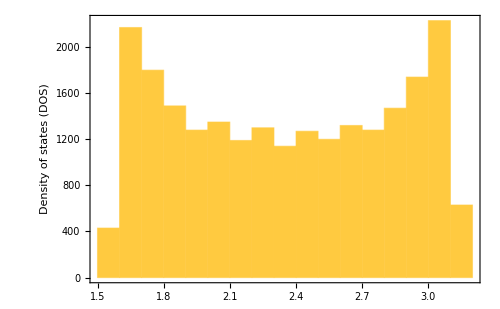

```mathematica
Histogram[filteredEigenphases,Automatic,"Intensity",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

```mathematica
unfoldedEigenphases=Unfold[filteredEigenphases];
```

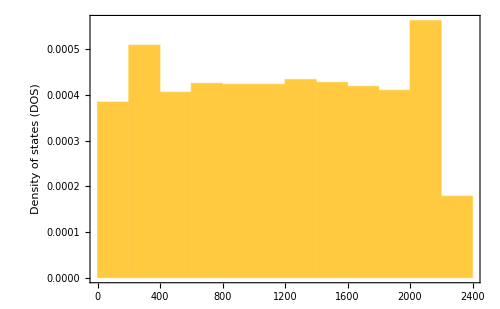

```mathematica
Histogram[unfoldedEigenphases["UnfoldedLevels"],Automatic,"PDF",
Frame->True,FrameLabel->{"", "Density of states (DOS)"},FrameStyle->Directive[Black,22],ImageSize->500
]
```

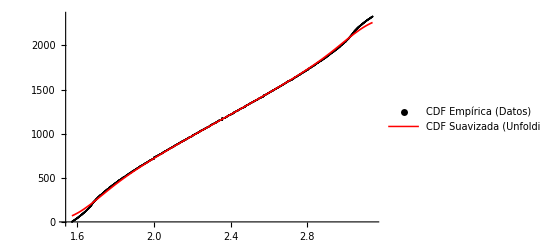

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
evals=unfoldedEigenphases["OriginalLevels"];
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[unfoldedEigenphases["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

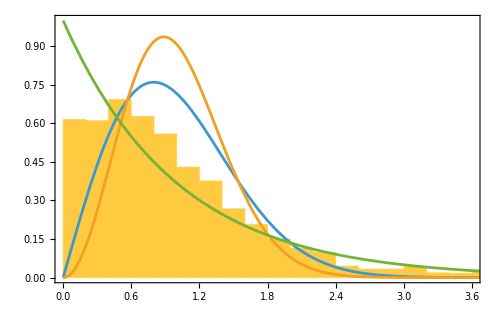

```mathematica
Show[
Histogram[Differences[unfoldedEigenphases["UnfoldedLevels"][[;;-200]]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π],Exp[-s]},{s,0,4.}]
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

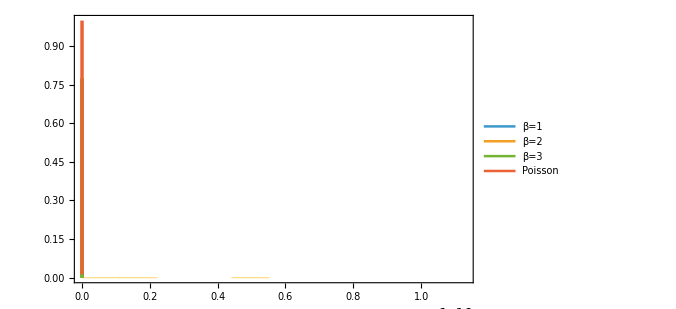

```mathematica
Show[
Histogram[SpacingRatios[filteredEigenphases,1],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,22],ImageSize->500],
Plot[Append[RatiosDistribution[r,#]&/@Range[3],RatiosDistributionPoisson[r,1]]//Evaluate,{r,0,8.},PlotLegends->Placed[Append["β="<>ToString[#]&/@Range[3],"Poisson"],{Right,Top}],PlotStyle->Directive[Thickness[0.005],Opacity[1.]],LabelStyle->Directive[20],PlotRange->All]
]
```

```mathematica
Table[EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,1.],RatiosDistribution[#,β]&],{β,3}]
```

{0.0361626,0.0639077,0.173755}

```mathematica
Table[EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,2.],RatiosDistribution[#,β]&],{β,3}]
```

{0.226943,0.0932235,0.0370469}

## 5. Preparing the Initial State

We will start with a Gaussian Wavepacket localized in the center of the stadium . The state is a vector of size $2N$ (Position $\otimes$ Spin) . We must normalize it so total probability $\sum | \psi | ^2 = 1 $ .

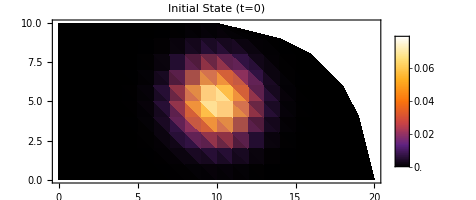

```mathematica
(*Helper to find the index of the center point*)
coords=billiardData["Coords"];
centerPoint={Floor[(xc+nu)/2],Floor[nu/2]}; (*Approximate center*)

(*Create a Gaussian envelope function*)
GaussianPacket[pos_]:=Exp[-Norm[pos-centerPoint]^2/(2.0*2.^2)];

(*Build the spatial vector*)
spatialAmplitudes=GaussianPacket/@coords;

(*Combine with an initial Spin UP state:{1,0}*)
(*We KroneckerProduct the spatial part with the spin part*)
psi0=Flatten[KroneckerProduct[spatialAmplitudes,{1,0} (*Spin Up*)]];

(*NORMALIZE the state*)
psi0=Normalize[psi0];

(*Visualize initial probability*)
ListDensityPlot[
Flatten/@Transpose[{coords,Partition[Abs[psi0]^2,2][[All,1]]+Partition[Abs[psi0]^2,2][[All,2]]}],
ColorFunction->"SunsetColors",PlotLabel->"Initial State (t=0)",PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic]
```

## 6. Time Evolution (The Walk)

Now we let the particle walk! We calculate the state for 30 time steps.We use NestList which is a functional way to do: $x_0, f(x_0), f(f(x_0))...$

```mathematica
(*Number of steps*)
tMax=30;

(*Evolve!*)
(*This applies EvolutionStep repeatedly to psi0*)
trajectory=NestList[U.#&,psi0,tMax];

Print["Simulation complete. Generated ",Length[trajectory]," states."];
```

Simulation complete. Generated 31 states.

## 7. Visualization and Analysis

Let’s look at the probability distribution $|\psi(t)|^2$ at the final step. In Quantum Walks, unlike classical random walks, you will see interference patterns and ballistic spreading (moving faster than diffusion).

```mathematica
(*Function to convert state vector to plot-able data*)
StateToPlotData[stateVector_,coordinates_]:=Module[
{probs},
(*1. Calculate|amplitude|^2*)
probs=Abs[stateVector]^2;
(*2. Sum Up and Down spin components for each site*)
(*The vector is {Site1_Up,Site1_Down,Site2_Up,Site2_Down...}*)
(*We partition by 2 and sum the sublists*)
probs=Total/@Partition[probs,2];
(*3. Combine with coordinates*)
MapThread[Append,{coordinates,probs}]
];
```

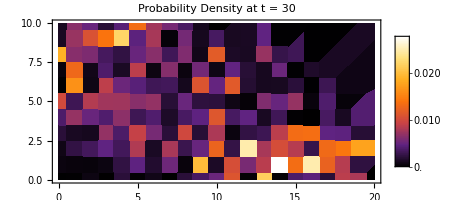

```mathematica
(*Plot the final state*)
finalPlotData=StateToPlotData[Last[trajectory],coords];

ListDensityPlot[finalPlotData,
ColorFunction->"SunsetColors",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
ListAnimate[ListDensityPlot[StateToPlotData[#,coords],
ColorFunction->"SunsetColors",PlotLabel->Row[{"Probability Density at t = ",tMax}],PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,InterpolationOrder->0]&/@trajectory]
```